## Model Building for y

```mathematica
Wallet = Import["/Users/dalila/TrainingWithNoNearzero.csv","CSV"]
```

```mathematica
Wallet= Wallet[[All,2;;]]
```

```mathematica
heading = Wallet[[1]]
```

{x002,x003,x004,x005,x006,x007,x008,x009,x010,x011,x012,x013,x014,x015,x016,x017,x018,x019,x020,x021,x022,x023,x024,x025,x026,x027,x028,x029,x030,x031,x032,x033,x034,x035,x036,x037,x038,x039,x040,x041,x042,x043,x044,x045,x046,x047,x048,x049,x050,x051,x052,x053,x054,x055,x056,x057,x058,x059,x061,x062,x063,x064,x065,x066,x071,x072,x073,x074,x075,x076,x080,x081,x082,x088,x089,x097,x098,x099,x104,x106,x107,x108,x110,x111,x112,x113,x114,x115,x116,x119,x120,x121,x126,x147,x148,x155,x162,x168,x169,x170,x171,x172,x173,x174,x177,x178,x179,x181,x182,x183,x184,x185,x186,x187,x188,x189,x190,x191,x192,x193,x194,x195,x196,x198,x199,x200,x201,x209,x210,x211,x222,x223,x224,x225,x226,x227,x228,x229,x230,x231,x232,x233,x234,x235,x236,x237,x238,x239,x240,x242,x244,x245,x246,x247,x248,x249,x250,x251,x253,x254,x255,x256,x257,x258,x259,x260,x261,x262,x263,x264,x265,x266,x267,x268,x269,x270,x271,x272,x273,x274,x275,x276,x277,x278,x279,x280,x281,x282,x283,x284,x285,x287,x288,x289,x290,x291,x292,x293,x294,x295,x296,x297,x298,x299,x300,x301,x302,x303,x304,y}

```mathematica
Dimensions[Wallet]
```

{100001,210}

find variables with missing values

```mathematica
Table[If[MemberQ[Wallet[[All,i]],"NA"],Wallet[[1,i]],Nothing],{i,210}]
```

{x002,x003,x004,x005,x041,x044,x045,x057,x058,x098,x148,x155,x162,x222,x223,x234,x235,x237,x238,x239,x242,x253,x255,x256,x257,x259,x265,x266,x267,x268,x272,x275,x287,x288,x289,x290,x293,x295,x297,x302,x304}

```mathematica
Length[%63]
```

41

```mathematica
VariablePosition[l_,heading_] := Flatten[Map[Position[heading,#]&,l]]
```

```mathematica
variablesWithMissingValues =VariablePosition[%63,heading]
```

{1,2,3,4,40,43,44,56,57,77,95,96,97,131,132,143,144,146,147,148,150,159,161,162,163,165,171,172,173,174,178,181,192,193,194,195,198,200,202,207,209}

find variables with less than 20,000 missing data points

```mathematica
Table[tp=Length[Cases[Wallet[[All,i]],"NA"]];If [tp < 20000,i,Nothing],{i,variablesWithMissingValues }]
```

{4,43,44,143,178}

show the variables name of the one to keep

```mathematica
heading[[{4,43,44,143,178}]]
```

{x005,x044,x045,x234,x272}

remove the variables with missing values to keep from the variables with missing values

```mathematica
Complement[variablesWithMissingValues ,%]
```

```mathematica
Length[{1,2,3,40,56,57,77,95,96,97,131,132,144,146,147,148,150,159,161,162,163,165,171,172,173,174,181,192,193,194,195,198,200,202,207,209}]
```

36

Finally decide on the variables to choose for modeling

```mathematica
Variables2Keep = Complement[heading,heading[[%]]]
```

```mathematica
Var2Keep={"x005","x006","x007","x008","x009","x010","x011","x012","x013","x014","x015","x016","x017","x018","x019","x020","x021","x022","x023","x024","x025","x026","x027","x028","x029","x030","x031","x032","x033","x034","x035","x036","x037","x038","x039","x040","x042","x043","x044","x045","x046","x047","x048","x049","x050","x051","x052","x053","x054","x055","x056","x059","x061","x062","x063","x064","x065","x066","x071","x072","x073","x074","x075","x076","x080","x081","x082","x088","x089","x097","x099","x104","x106","x107","x108","x110","x111","x112","x113","x114","x115","x116","x119","x120","x121","x126","x147","x168","x169","x170","x171","x172","x173","x174","x177","x178","x179","x181","x182","x183","x184","x185","x186","x187","x188","x189","x190","x191","x192","x193","x194","x195","x196","x198","x199","x200","x201","x209","x210","x211","x224","x225","x226","x227","x228","x229","x230","x231","x232","x233","x234","x236","x240","x244","x245","x246","x247","x248","x249","x250","x251","x254","x258","x260","x261","x262","x263","x264","x269","x270","x271","x272","x273","x274","x276","x277","x278","x279","x280","x281","x282","x283","x284","x285","x291","x292","x294","x296","x298","x299","x300","x301","x303","y"}
```

```mathematica
variableIndex = VariablePosition[Variables2Keep,heading]
```

```mathematica
VariableIndex ={4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,133,134,135,136,137,138,139,140,141,142,143,145,149,151,152,153,154,155,156,157,158,160,164,166,167,168,169,170,175,176,177,178,179,180,182,183,184,185,186,187,188,189,190,191,196,197,199,201,203,204,205,206,208,210}
```

Create a new variable WalletData from Wallet with only the variables needed for building the model

```mathematica
WalletData= Wallet[[All,variableIndex ]]
```

```mathematica
Dimensions[WalletData]
```

{100001,174}

Replace NA with “Missing”.  This step is not necessary

```mathematica
WalletWithMissingVal = ReplaceAll[WalletData,"NA"-> "Missing"]
```

Prepare the training set and the validation set

```mathematica
l = Dimensions[WalletWithMissingVal ][[1]]
trainNdx =RandomInteger[{1,l},30000]
training= WalletWithMissingVal [[trainNdx,All]]
training = Map[Rule[Most[#],Last[#]]&,training]
left = Complement[Range[l],trainNdx]
ValNdx = RandomInteger[{1,Length[left]},5000]
validation =WalletWithMissingVal [[ValNdx,All]];
validation = Map[Rule[Most[#],Last[#]]&,validation];
```

## Model Building

First model: Extreme Gradient Boosted Trees Model with number of rounds - 300, maximum depth of 16, and L2 regularization of 0.5

```mathematica
pWithMissing = Predict[training,Method->{"GradientBoostedTrees",MaxTrainingRounds-> 300,
"MaxDepth"->16,"LeavesNumber"-> 25,"LeafSize"-> 35,"L2Regularization"-> 0.5},ValidationSet-> validation[[;;5000,All]]]
```

PredictorFunction[…]

```mathematica
PredictorInformation[pWithMissing]
```

Predictor information
Input type | Mixed (number: 173)
Method | GradientBoostedTrees
Standard deviation | 28.2 ± 0.64
Loss | 5.09 ± 0.053
Single evaluation time | 35.3 ms/example
Batch evaluation speed | 719. examples/s
Predictor memory | 5.35 MB
Training examples used | 30000 examples
Training time | 2 0
 |

The RMSE and MAE are 708.747 and 19.4422 Respectively.  Performance of the model with validation set.  One can see that the residuals have no pattern, and they are normally distributed, the actual and predicted value are mostly on the 45% line. However, the model is more optimistic when actual values are less than 400.

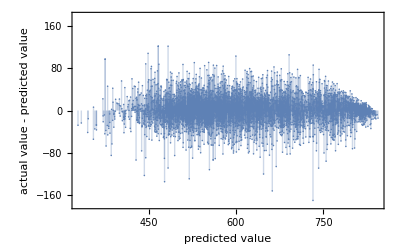
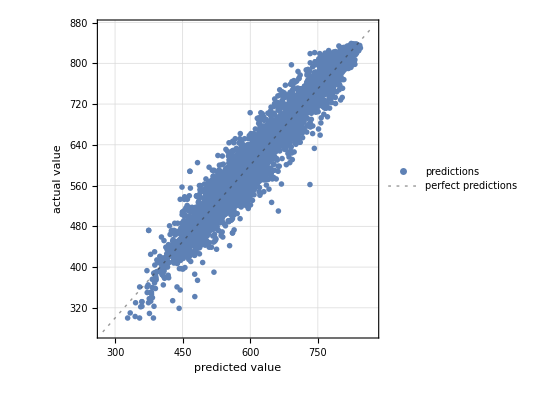
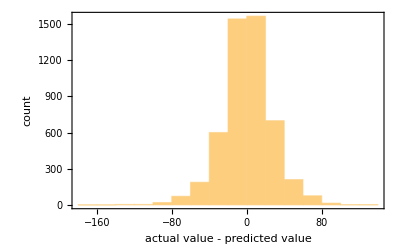
{-Graphics-,-Graphics-,-Graphics-,708.747,19.4421}

```mathematica
PredictorMeasurements[pWithMissing,validation,{"ResidualPlot","ComparisonPlot","ResidualHistogram","MeanSquare","MeanDeviation"}]
```

The Mean Absolute Percentage Error for the validation set is 2.93964

```mathematica
DumpSave
```

```mathematica
result = Map[pWithMissing[#[[1]]]&,validation];
l= Length[result];
100*Total[Abs[(validation[[All,2]]-result)/validation[[All,2]]]]/l
```

2.93964

Build a second model with L1 = 0.7 and L2 = 0.7 and learning rate of 0.2

```mathematica
pWithMissing = Predict[training,Method->{"GradientBoostedTrees","MaxDepth"-> 150,MaxTrainingRounds->750,"L1Regularization"->0.7,"L2Regularization"-> 0.7}]
```

PredictorFunction[…]

This model has lower RMSE and MAE than the previous one 686.497 and 17.2478 respectively.

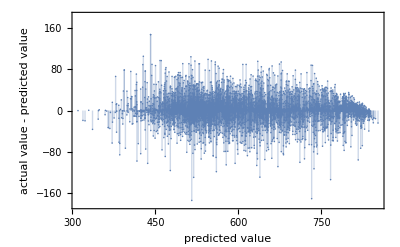
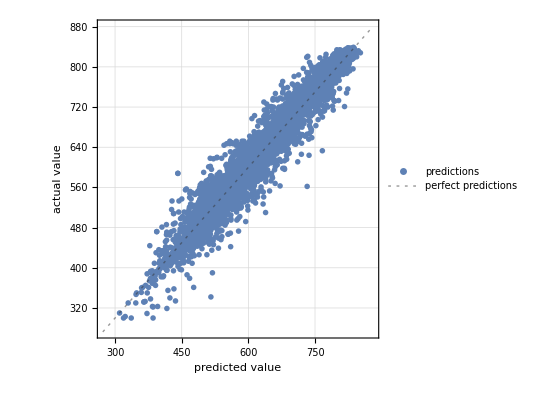
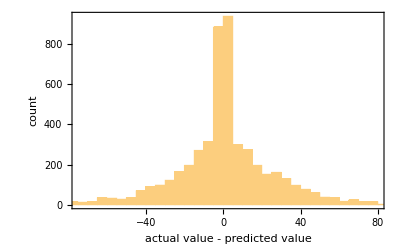
{-Graphics-,-Graphics-,-Graphics-,686.497,17.2478}

```mathematica
PredictorMeasurements[pWithMissing,validation,{"ResidualPlot","ComparisonPlot","ResidualHistogram","MeanSquare","MeanDeviation"}]
```

```mathematica
Sqrt[686.497]
```

26.2011

Save the model

```mathematica
DumpSave["BestWalletModel.mx",pWithMissing]
```

{PredictorFunction[…]}

Upload the model.

```mathematica
<< "/Users/dalila/Documents/walletFold/BestWalletModel.mx"
```

Model information

```mathematica
PredictorInformation[pWithMissing]
```

Predictor information
Input type | Mixed (number: 173)
Method | GradientBoostedTrees
Standard deviation | 27.5 ± 0.66
Loss | 72.5 ± 2.9
Single evaluation time | 67.9 ms/example
Batch evaluation speed | 198. examples/s
Predictor memory | 7.02 MB
Training examples used | 30000 examples
Training time | 1 55
 |

Test Model with Test Data

```mathematica
Var2Keep={"x005","x006","x007","x008","x009","x010","x011","x012","x013","x014","x015","x016","x017","x018","x019","x020","x021","x022","x023","x024","x025","x026","x027","x028","x029","x030","x031","x032","x033","x034","x035","x036","x037","x038","x039","x040","x042","x043","x044","x045","x046","x047","x048","x049","x050","x051","x052","x053","x054","x055","x056","x059","x061","x062","x063","x064","x065","x066","x071","x072","x073","x074","x075","x076","x080","x081","x082","x088","x089","x097","x099","x104","x106","x107","x108","x110","x111","x112","x113","x114","x115","x116","x119","x120","x121","x126","x147","x168","x169","x170","x171","x172","x173","x174","x177","x178","x179","x181","x182","x183","x184","x185","x186","x187","x188","x189","x190","x191","x192","x193","x194","x195","x196","x198","x199","x200","x201","x209","x210","x211","x224","x225","x226","x227","x228","x229","x230","x231","x232","x233","x234","x236","x240","x244","x245","x246","x247","x248","x249","x250","x251","x254","x258","x260","x261","x262","x263","x264","x269","x270","x271","x272","x273","x274","x276","x277","x278","x279","x280","x281","x282","x283","x284","x285","x291","x292","x294","x296","x298","x299","x300","x301","x303"}
```

```mathematica
heading ={"x002","x003","x004","x005","x006","x007","x008","x009","x010","x011","x012","x013","x014","x015","x016","x017","x018","x019","x020","x021","x022","x023","x024","x025","x026","x027","x028","x029","x030","x031","x032","x033","x034","x035","x036","x037","x038","x039","x040","x041","x042","x043","x044","x045","x046","x047","x048","x049","x050","x051","x052","x053","x054","x055","x056","x057","x058","x059","x061","x062","x063","x064","x065","x066","x071","x072","x073","x074","x075","x076","x080","x081","x082","x088","x089","x097","x098","x099","x104","x106","x107","x108","x110","x111","x112","x113","x114","x115","x116","x119","x120","x121","x126","x147","x148","x155","x162","x168","x169","x170","x171","x172","x173","x174","x177","x178","x179","x181","x182","x183","x184","x185","x186","x187","x188","x189","x190","x191","x192","x193","x194","x195","x196","x198","x199","x200","x201","x209","x210","x211","x222","x223","x224","x225","x226","x227","x228","x229","x230","x231","x232","x233","x234","x235","x236","x237","x238","x239","x240","x242","x244","x245","x246","x247","x248","x249","x250","x251","x253","x254","x255","x256","x257","x258","x259","x260","x261","x262","x263","x264","x265","x266","x267","x268","x269","x270","x271","x272","x273","x274","x275","x276","x277","x278","x279","x280","x281","x282","x283","x284","x285","x287","x288","x289","x290","x291","x292","x293","x294","x295","x296","x297","x298","x299","x300","x301","x302","x303","x304","y"}
```

Test model with unseen data

```mathematica
TestData = Import["/Users/dalila/Documents/walletFold/Data Scientist Test/walletTestingSet.csv"]
```

```mathematica
testHead = TestData[[1,1;;]]
```

```mathematica
TestData= TestData[[2;;,2;;]]
```

```mathematica
varPos =VariablePosition[{"x005","x006","x007","x008","x009","x010","x011","x012","x013","x014","x015","x016","x017","x018","x019","x020","x021","x022","x023","x024","x025","x026","x027","x028","x029","x030","x031","x032","x033","x034","x035","x036","x037","x038","x039","x040","x042","x043","x044","x045","x046","x047","x048","x049","x050","x051","x052","x053","x054","x055","x056","x059","x061","x062","x063","x064","x065","x066","x071","x072","x073","x074","x075","x076","x080","x081","x082","x088","x089","x097","x099","x104","x106","x107","x108","x110","x111","x112","x113","x114","x115","x116","x119","x120","x121","x126","x147","x168","x169","x170","x171","x172","x173","x174","x177","x178","x179","x181","x182","x183","x184","x185","x186","x187","x188","x189","x190","x191","x192","x193","x194","x195","x196","x198","x199","x200","x201","x209","x210","x211","x224","x225","x226","x227","x228","x229","x230","x231","x232","x233","x234","x236","x240","x244","x245","x246","x247","x248","x249","x250","x251","x254","x258","x260","x261","x262","x263","x264","x269","x270","x271","x272","x273","x274","x276","x277","x278","x279","x280","x281","x282","x283","x284","x285","x291","x292","x294","x296","x298","x299","x300","x301","x303","y"},testHead]
```

```mathematica
testD =TestData[[All,varPos]]
```

```mathematica
Dimensions[testD]
```

{30000,174}

```mathematica
testD = ReplaceAll[testD,"NA"-> "Missing"] ;
```

```mathematica
result = Timing[Map[pWithMissing[#]&,testD[[All,;;173]]]]
```

{20322.3,{705.246,524.237,552.493,677.436,799.548,501.714,519.666,29986,580.316,516.452,377.526,487.303,814.976,423.634,397.925}}
 |  |  |  |

```mathematica
testRule = Map[Rule[Most[#],Last[#]]&,testD]
```

Model performance:  As one can see RMSE and MAE are very similar to the results found on the validation set.  The residuals histogram still look like a normal distribution.

```mathematica
PredictorMeasurements[pWithMissing,testRule,{"ResidualPlot","ComparisonPlot","ResidualHistogram","MeanSquare","MeanDeviation"}]
```

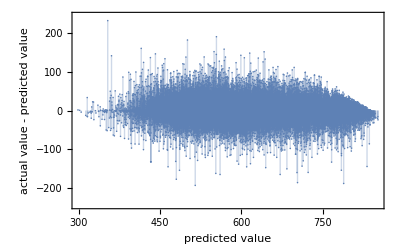
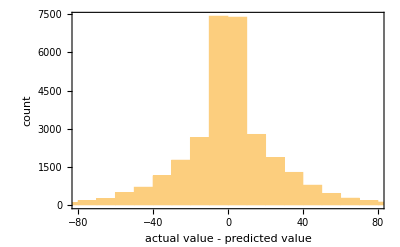
```mathematica
{-Graphics-,,-Graphics-,713.6640026978447,17.358247690650263}
```

Calculate the time to perform 100 predictions

```mathematica
AbsoluteTiming[pWithMissing[testD[[1;;100,;;173]]]]
```

{0.124054,{705.246,524.237,552.493,677.436,799.548,501.714,519.666,500.735,534.014,466.212,786.494,815.892,784.847,635.885,808.195,535.16,660.301,527.495,629.331,703.938,611.982,768.707,401.789,583.892,706.654,829.392,632.504,583.848,666.236,826.814,524.615,765.587,614.587,592.209,520.973,590.153,725.779,677.429,619.704,742.806,481.271,604.245,460.186,767.43,701.216,448.416,730.469,558.049,753.601,482.636,528.171,498.058,818.185,537.294,478.992,667.98,582.504,617.338,680.64,521.242,497.925,758.624,734.916,753.464,522.234,624.841,675.436,765.274,793.125,517.831,607.542,827.237,519.293,591.147,489.756,454.276,511.571,497.761,477.817,815.325,821.482,437.999,642.424,596.872,514.335,510.698,620.282,705.94,561.407,564.975,661.542,468.189,805.803,518.263,570.537,802.229,741.442,681.89,685.757,508.859}}

MAPE is still under 3 or 2.95047

```mathematica
l= Length[r];
100*Total[Abs[(testD[[All,174]]-r)/testD[[All,174]]]]/l
```

2.95047

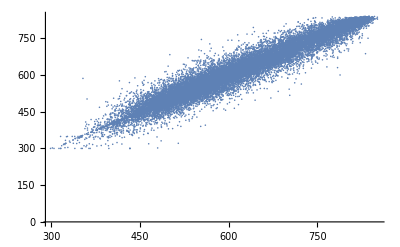

```mathematica
ListPlot[MapThread[List,{r,testD[[All,174]]}]]
```

## Build an API

```mathematica
predictVal[st_] := Module[{tmp = st,l},
tmp = StringSplit[tmp,";"];
tmp = ReplaceAll[tmp,";"-> "" ];
tmp = Map[ToExpression[StringSplit[#,","]]&,tmp];
StringJoin[ToString[Map[pWithMissing[#]&,tmp]]]
]
```

```mathematica
DumpSave["DumpModelAPI.mx",{pWithMissing,predictVal,s,testD}]
```

```mathematica
predictAPI = APIFunction[{"s"->"String"},predictVal[#s]&,"JSON"]
```

APIFunction[{s→String},predictVal[#s]&,JSON]

```mathematica
EmbedCode[predictAPI,"Python"]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from Python:
Code
 | Copy to Clipboard
from __future__ import unicode_literals

import sys

if sys.version_info[0] == 2:
    from urllib import urlencode
    from urllib2 import urlopen
else:
    from urllib.parse import urlencode
    from urllib.request import urlopen

def wolfram_cloud_call(**args):
    result = urlopen('http://www.wolframcloud.com/objects/61bdcda0-9ea3-4de7-a4fb-b01af222d267', urlencode(args).encode('utf-8'))
    return result.read()

def call(s):
    textresult = wolfram_cloud_call(s=s)
    return textresult

```mathematica
EmbedCode[APIFunction["d"-> "String",predictVal[#d]&,{"JSON","WL"}],"Python"]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from Python:
Code
 | Copy to Clipboard
from __future__ import unicode_literals

import sys

if sys.version_info[0] == 2:
    from urllib import urlencode
    from urllib2 import urlopen
else:
    from urllib.parse import urlencode
    from urllib.request import urlopen

def wolfram_cloud_call(**args):
    result = urlopen('http://www.wolframcloud.com/objects/a3fcf3f4-c5ec-4115-aa3f-40b23d54c187', urlencode(args).encode('utf-8'))
    return result.read()

def call(d):
    textresult = wolfram_cloud_call(d=d)
    return textresult

```mathematica
Export["Var2Keep.xls",Var2Keep,"XLS"]
```

Var2Keep.xls